```mathematica
Box 1 : This file estimates the concentration of dimer (and other intermediates) in the dimerization reaction, Supplementary note 14.
```

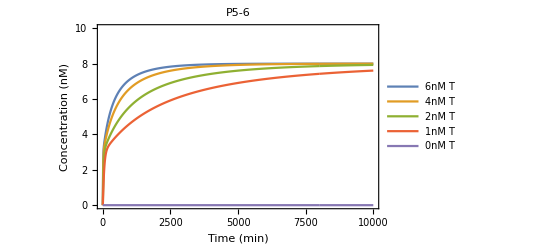

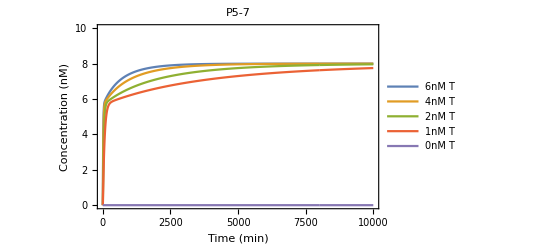

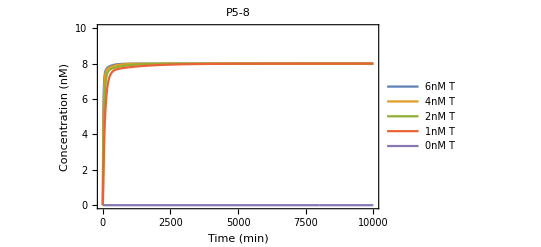

```mathematica
Btype={"B1","B1a","B1b"};
Ptype={"P29-5","P28-5","P27-5"};
Mtype={"M1M2","M1aM2","M1bM2"};
MPtype={"P5-6","P5-7","P5-8"};
For[Ii=1,Ii<=1,Ii++,
For[J=1,J<=3,J++,
type=Btype[[Ii]];
ty=Mtype[[Ii]];
proof=Ptype[[J]];
mproof=MPtype[[J]];
tend=10000;
Clear[a,b,c,x,y,z,k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,t,C1,C2,C3,C4,C5,C6,C3a,C1a];
SetDirectory[ParentDirectory[NotebookDirectory[]]];
(*Import all rates*)
k1=Import["1. Lock opening and binding\\Rates\\"<>type<>"klock.wl"][[1]];
k2=Import["1. Lock opening and binding\\Rates\\"<>type<>"klock.wl"][[2]];
k3=Import["BT+P rates\\"<>type<>proof<>".wl"][[1]];
k4=Import["BT+P rates\\"<>type<>proof<>".wl"][[2]];
k7=Import["BT+P rates\\"<>type<>proof<>".wl"][[3]];
(*k3=kproof[[J]][[Ii]];
k4=kproof2[[J]][[Ii]];*)
k5=0;k6=0;k7=0;
k8=Import["C:\\Users\\asengar\\My Drive\\Ubuntu\\Rakesh\\Dimerisation with kp\\"<>Mtype[[Ii]]<>"(dimer)_rates.wl"][[1]];
k9=Import["C:\\Users\\asengar\\My Drive\\Ubuntu\\Rakesh\\Dimerisation with kp\\"<>Mtype[[Ii]]<>"(dimer)_rates.wl"][[2]];
k8=0.007*3;
k9=0;
k10=0;
k11=0;
(*Print["Lock opening: ",k1, ". Lock closing: ",k2, ". Proofreader f:",k3,". Proofreader b:",k4,". Dimer rate: ",k8 ];*)
(*C1: concentration with domain B/M: ML, MT,m MP, MPR, MN (dimer), MNR(dimer with reporter: [ML]o*)
(*C2: Concentration with domain P: P, MP, MPR, PR:[Po]*)
(*C3: Concentration with domain T: MT, T:{1,2,4,6}*)
(*C4: Concentration with domain R: MNR, RQ, MPR, PR: [RQ]o*)
(*C5: Concentration with domain Q: RQ, Q: [RQ]o*)
(*C6: Concentration with domain L: ML, L: [ML]o*)
(*C7: Concentration with domain N: N, MN, MNR: [N]o*)
(*x:[MT], y: [MP]; z: [MPR], a: [PR], b: [MN], c: [MNR]*)
(* [ML]=C1-x-y-z-b-c;
[T]=C3-x;
[L]=C6-[ML]=C6-C1+x+y+z+b+c;
[P]=C2-y-z-a;
[RQ]=C4-a-c-z;
[Q]=C5-[RQ]=C5-C4+a+c+z
[N]=C7-b-c
*)
concT={6,4,2,1,0};
RQo=0;
Po=50;
data={Table[t,{t,0,tend}]};(*Stores [MN]*)
data2=data;
data3=data;
data4=data;
data5=data;
For[i=1,i<=Length[concT],i++,
C1=8;
C6=8;
C2=Po;
C3=concT[[i]];
C4=RQo;
C5=RQo;
C7=10;
(*ODE model*)
sol=NDSolve[{x'[t]==k1*(C1-x[t]-y[t]-z[t]-b[t]-c[t])*(C3-x[t])-k2*x[t]*(C6-C1+x[t]+y[t]+z[t]+b[t]+c[t])-k3*x[t]*(C2-a[t]-y[t]-z[t])+k4*y[t]*(C3-x[t])-k8*x[t]*(C7-b[t]-c[t])+k9*b[t]*(C3-x[t]),

y'[t]==k3*x[t]*(C2-a[t]-y[t]-z[t])-k4*y[t]*(C3-x[t])-k5*y[t]*(C4-z[t]-a[t]-c[t])+k6*z[t]*(C5-C4+z[t]+a[t]+c[t]),

z'[t]==k5*y[t]*(C4-z[t]-a[t]-c[t])-k6*z[t]*(C5-C4+z[t]+a[t]+c[t]),

a'[t]==k7*(C2-y[t]-z[t]-a[t])*(C4-a[t]-c[t]-z[t]),

b'[t]==k8*x[t]*(C7-b[t]-c[t])-k9*b[t]*(C3-x[t])-k10*b[t]*(C4-a[t]-c[t]-z[t])+k11*c[t]*(C5-C4+z[t]+a[t]+c[t]),

c'[t]==k10*b[t]*(C4-a[t]-c[t]-z[t])-k11*c[t]*(C5-C4+z[t]+a[t]+c[t])
,
x[0]==0,y[0]==0,z[0]==0,a[0]==0,b[0]==0,c[0]==0},{x,y,z,a,b,c},{t,0,tend}];
(*x:[MT], y: [MP]; z: [MPR], a: [PR], b: [MN], c: [MNR]*)
AppendTo[data,Table[(C1-x[t]-y[t]-z[t]-b[t]-c[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data2,Table[(x[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data3,Table[(y[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data4,Table[(b[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data5,Table[(k3*x[t]*(C2-a[t]-y[t]-z[t])-k4*y[t]*(C3-x[t]))/.sol[[1]],{t,0,tend}]];

(*
AppendTo[data,Table[{t,(y[t])/.sol[[1]],(C1-x[t]-y[t]-z[t]-b[t]-c[t])/.sol[[1]]},{t,0,tend}]];*)

];

s=ListPlot[data4[[2;;6]],Joined->True,PlotRange->{0,10},PlotLabel->mproof,Frame->True,FrameLabel->{"Time (min)","Concentration (nM)"},BaseStyle->14,PlotLegends->{"6nM T","4nM T","2nM T","1nM T","0nM T"}];
Print[s]

(*Ucomment this*);
SetDirectory["Dimer Prediction"];
Export[type<>proof<>".xlsx",Transpose[data4]]
]]
```

```mathematica
Box 2 : This file estimates the concentration of dimer (and other intermediates) in the dimerization reaction with proofreader conc = 0
```

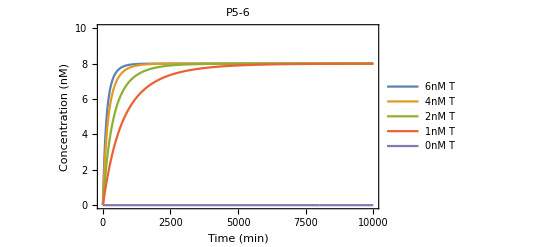

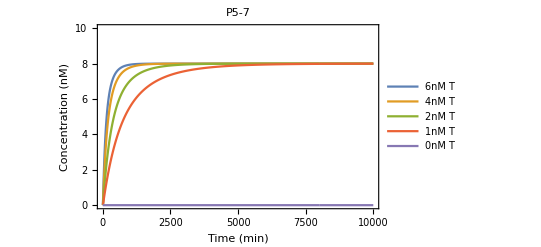

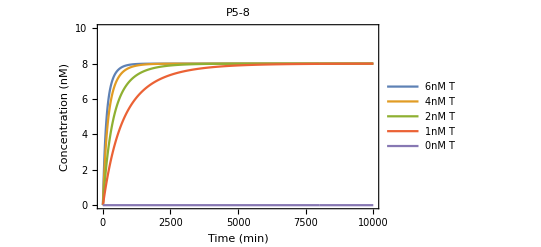

```mathematica
Btype={"B1","B1a","B1b"};
Ptype={"P29-5","P28-5","P27-5"};
Mtype={"M1M2","M1aM2","M1bM2"};
MPtype={"P5-6","P5-7","P5-8"};
For[Ii=3,Ii<=3
,Ii++,
For[J=1,J<=3,J++,

type=Btype[[Ii]];
ty=Mtype[[Ii]];
proof=Ptype[[J]];
mproof=MPtype[[J]];
tend=10000;
Clear[a,b,c,x,y,z,k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,t,C1,C2,C3,C4,C5,C6,C3a,C1a];
SetDirectory[ParentDirectory[NotebookDirectory[]]];
(*Import all rates*)
k1=Import["1. Lock opening and binding\\Rates\\"<>type<>"klock.wl"][[1]];
k2=Import["1. Lock opening and binding\\Rates\\"<>type<>"klock.wl"][[2]];
k3=Import["BT+P rates\\"<>type<>proof<>".wl"][[1]];
k4=Import["BT+P rates\\"<>type<>proof<>".wl"][[2]];
k7=Import["BT+P rates\\"<>type<>proof<>".wl"][[3]];
(*k3=kproof[[J]][[Ii]];
k4=kproof2[[J]][[Ii]];*)
k5=0;k6=0;k7=0;
k8=Import["C:\\Users\\asengar\\My Drive\\Ubuntu\\Rakesh\\Dimerisation with kp\\"<>Mtype[[Ii]]<>"(dimer)_rates.wl"][[1]];
k9=Import["C:\\Users\\asengar\\My Drive\\Ubuntu\\Rakesh\\Dimerisation with kp\\"<>Mtype[[Ii]]<>"(dimer)_rates.wl"][[2]];
k8=0.007*3;
k9=0;
k10=0;
k11=0;
(*Print["Lock opening: ",k1, ". Lock closing: ",k2, ". Proofreader f:",k3,". Proofreader b:",k4,". Dimer rate: ",k8 ];*)
(*C1: concentration with domain B/M: ML, MT,m MP, MPR, MN (dimer), MNR(dimer with reporter: [ML]o*)
(*C2: Concentration with domain P: P, MP, MPR, PR:[Po]*)
(*C3: Concentration with domain T: MT, T:{1,2,4,6}*)
(*C4: Concentration with domain R: MNR, RQ, MPR, PR: [RQ]o*)
(*C5: Concentration with domain Q: RQ, Q: [RQ]o*)
(*C6: Concentration with domain L: ML, L: [ML]o*)
(*C7: Concentration with domain N: N, MN, MNR: [N]o*)
(*x:[MT], y: [MP]; z: [MPR], a: [PR], b: [MN], c: [MNR]*)
(* [ML]=C1-x-y-z-b-c;
[T]=C3-x;
[L]=C6-[ML]=C6-C1+x+y+z+b+c;
[P]=C2-y-z-a;
[RQ]=C4-a-c-z;
[Q]=C5-[RQ]=C5-C4+a+c+z
[N]=C7-b-c
*)
concT={6,4,2,1,0};
RQo=0;
Po=0;
data={Table[t,{t,0,tend}]};(*Stores [MN]*)
data2=data;
data3=data;
data4=data;
data5=data;
For[i=1,i<=Length[concT],i++,
C1=8;
C6=8;
C2=Po;
C3=concT[[i]];
C4=RQo;
C5=RQo;
C7=10;
(*ODE model*)
sol=NDSolve[{x'[t]==k1*(C1-x[t]-y[t]-z[t]-b[t]-c[t])*(C3-x[t])-k2*x[t]*(C6-C1+x[t]+y[t]+z[t]+b[t]+c[t])-k3*x[t]*(C2-a[t]-y[t]-z[t])+k4*y[t]*(C3-x[t])-k8*x[t]*(C7-b[t]-c[t])+k9*b[t]*(C3-x[t]),

y'[t]==k3*x[t]*(C2-a[t]-y[t]-z[t])-k4*y[t]*(C3-x[t])-k5*y[t]*(C4-z[t]-a[t]-c[t])+k6*z[t]*(C5-C4+z[t]+a[t]+c[t]),

z'[t]==k5*y[t]*(C4-z[t]-a[t]-c[t])-k6*z[t]*(C5-C4+z[t]+a[t]+c[t]),

a'[t]==k7*(C2-y[t]-z[t]-a[t])*(C4-a[t]-c[t]-z[t]),

b'[t]==k8*x[t]*(C7-b[t]-c[t])-k9*b[t]*(C3-x[t])-k10*b[t]*(C4-a[t]-c[t]-z[t])+k11*c[t]*(C5-C4+z[t]+a[t]+c[t]),

c'[t]==k10*b[t]*(C4-a[t]-c[t]-z[t])-k11*c[t]*(C5-C4+z[t]+a[t]+c[t])
,
x[0]==0,y[0]==0,z[0]==0,a[0]==0,b[0]==0,c[0]==0},{x,y,z,a,b,c},{t,0,tend}];
(*x:[MT], y: [MP]; z: [MPR], a: [PR], b: [MN], c: [MNR]*)
AppendTo[data,Table[(C1-x[t]-y[t]-z[t]-b[t]-c[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data2,Table[(x[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data3,Table[(y[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data4,Table[(b[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data5,Table[(k3*x[t]*(C2-a[t]-y[t]-z[t])-k4*y[t]*(C3-x[t]))/.sol[[1]],{t,0,tend}]];

(*
AppendTo[data,Table[{t,(y[t])/.sol[[1]],(C1-x[t]-y[t]-z[t]-b[t]-c[t])/.sol[[1]]},{t,0,tend}]];*)

];

s=ListPlot[data4[[2;;6]],Joined->True,PlotRange->{0,10},PlotLabel->mproof,Frame->True,FrameLabel->{"Time (min)","Concentration (nM)"},BaseStyle->14,PlotLegends->{"6nM T","4nM T","2nM T","1nM T","0nM T"}];
Print[s]

(*Ucomment this*);
SetDirectory["Dimer Prediction (P=0)"];
Export[type<>proof<>".xlsx",Transpose[data4]]
]]
```

```mathematica
Box 3: This file estimates the concentration of dimer (and other intermediates) in the dimerization reaction with backfward proofreader rate = 0
```

```mathematica
Btype={"B1","B1a","B1b"};
Ptype={"P29-5","P28-5","P27-5"};
Mtype={"M1M2","M1aM2","M1bM2"};
MPtype={"P5-6","P5-7","P5-8"};
For[Ii=1,Ii<=1,Ii++,
For[J=1,J<=3,J++,
type=Btype[[Ii]];
ty=Mtype[[Ii]];
proof=Ptype[[J]];
mproof=MPtype[[J]];
tend=10000;
Clear[a,b,c,x,y,z,k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,t,C1,C2,C3,C4,C5,C6,C3a,C1a];
SetDirectory[ParentDirectory[NotebookDirectory[]]];
(*Import all rates*)
k1=Import["1. Lock opening and binding\\Rates\\"<>type<>"klock.wl"][[1]];
k2=Import["1. Lock opening and binding\\Rates\\"<>type<>"klock.wl"][[2]];
k3=Import["BT+P rates\\"<>type<>proof<>".wl"][[1]];
k4=Import["BT+P rates\\"<>type<>proof<>".wl"][[2]];
k4=0;
k7=Import["BT+P rates\\"<>type<>proof<>".wl"][[3]];
(*k3=kproof[[J]][[Ii]];
k4=kproof2[[J]][[Ii]];*)
k5=0;k6=0;k7=0;
k8=Import["C:\\Users\\asengar\\My Drive\\Ubuntu\\Rakesh\\Dimerisation with kp\\"<>Mtype[[Ii]]<>"(dimer)_rates.wl"][[1]];
k9=Import["C:\\Users\\asengar\\My Drive\\Ubuntu\\Rakesh\\Dimerisation with kp\\"<>Mtype[[Ii]]<>"(dimer)_rates.wl"][[2]];
k8=0.007*3;
k9=0;
k10=0;
k11=0;
(*Print["Lock opening: ",k1, ". Lock closing: ",k2, ". Proofreader f:",k3,". Proofreader b:",k4,". Dimer rate: ",k8 ];*)
(*C1: concentration with domain B/M: ML, MT,m MP, MPR, MN (dimer), MNR(dimer with reporter: [ML]o*)
(*C2: Concentration with domain P: P, MP, MPR, PR:[Po]*)
(*C3: Concentration with domain T: MT, T:{1,2,4,6}*)
(*C4: Concentration with domain R: MNR, RQ, MPR, PR: [RQ]o*)
(*C5: Concentration with domain Q: RQ, Q: [RQ]o*)
(*C6: Concentration with domain L: ML, L: [ML]o*)
(*C7: Concentration with domain N: N, MN, MNR: [N]o*)
(*x:[MT], y: [MP]; z: [MPR], a: [PR], b: [MN], c: [MNR]*)
(* [ML]=C1-x-y-z-b-c;
[T]=C3-x;
[L]=C6-[ML]=C6-C1+x+y+z+b+c;
[P]=C2-y-z-a;
[RQ]=C4-a-c-z;
[Q]=C5-[RQ]=C5-C4+a+c+z
[N]=C7-b-c
*)
concT={6,4,2,1,0};
RQo=0;
Po=50;
data={Table[t,{t,0,tend}]};(*Stores [MN]*)
data2=data;
data3=data;
data4=data;
data5=data;
For[i=1,i<=Length[concT],i++,
C1=8;
C6=8;
C2=Po;
C3=concT[[i]];
C4=RQo;
C5=RQo;
C7=10;
(*ODE model*)
sol=NDSolve[{x'[t]==k1*(C1-x[t]-y[t]-z[t]-b[t]-c[t])*(C3-x[t])-k2*x[t]*(C6-C1+x[t]+y[t]+z[t]+b[t]+c[t])-k3*x[t]*(C2-a[t]-y[t]-z[t])+k4*y[t]*(C3-x[t])-k8*x[t]*(C7-b[t]-c[t])+k9*b[t]*(C3-x[t]),

y'[t]==k3*x[t]*(C2-a[t]-y[t]-z[t])-k4*y[t]*(C3-x[t])-k5*y[t]*(C4-z[t]-a[t]-c[t])+k6*z[t]*(C5-C4+z[t]+a[t]+c[t]),

z'[t]==k5*y[t]*(C4-z[t]-a[t]-c[t])-k6*z[t]*(C5-C4+z[t]+a[t]+c[t]),

a'[t]==k7*(C2-y[t]-z[t]-a[t])*(C4-a[t]-c[t]-z[t]),

b'[t]==k8*x[t]*(C7-b[t]-c[t])-k9*b[t]*(C3-x[t])-k10*b[t]*(C4-a[t]-c[t]-z[t])+k11*c[t]*(C5-C4+z[t]+a[t]+c[t]),

c'[t]==k10*b[t]*(C4-a[t]-c[t]-z[t])-k11*c[t]*(C5-C4+z[t]+a[t]+c[t])
,
x[0]==0,y[0]==0,z[0]==0,a[0]==0,b[0]==0,c[0]==0},{x,y,z,a,b,c},{t,0,tend}];
(*x:[MT], y: [MP]; z: [MPR], a: [PR], b: [MN], c: [MNR]*)
AppendTo[data,Table[(C1-x[t]-y[t]-z[t]-b[t]-c[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data2,Table[(x[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data3,Table[(y[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data4,Table[(b[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data5,Table[(k3*x[t]*(C2-a[t]-y[t]-z[t])-k4*y[t]*(C3-x[t]))/.sol[[1]],{t,0,tend}]];

(*
AppendTo[data,Table[{t,(y[t])/.sol[[1]],(C1-x[t]-y[t]-z[t]-b[t]-c[t])/.sol[[1]]},{t,0,tend}]];*)

];

s=ListPlot[data4[[2;;6]],Joined->True,PlotRange->{0,10},PlotLabel->mproof,Frame->True,FrameLabel->{"Time (min)","Concentration (nM)"},BaseStyle->14,PlotLegends->{"6nM T","4nM T","2nM T","1nM T","0nM T"}];
Print[s]

(*Ucomment this*);
SetDirectory["Dimer Prediction (k4=0)"];
Export[type<>proof<>".xlsx",Transpose[data4]]
]]
```